```mathematica
SetDirectory["/home/uyras/projects/spinIceStatSumm2/build-spinIceStatSumm2-Desktop_Qt_5_4_0_GCC_64bit-Debug"];
```

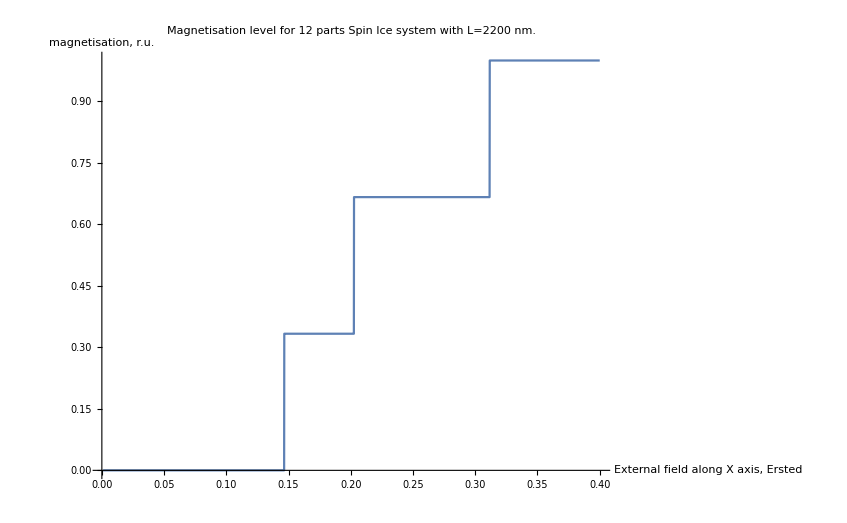

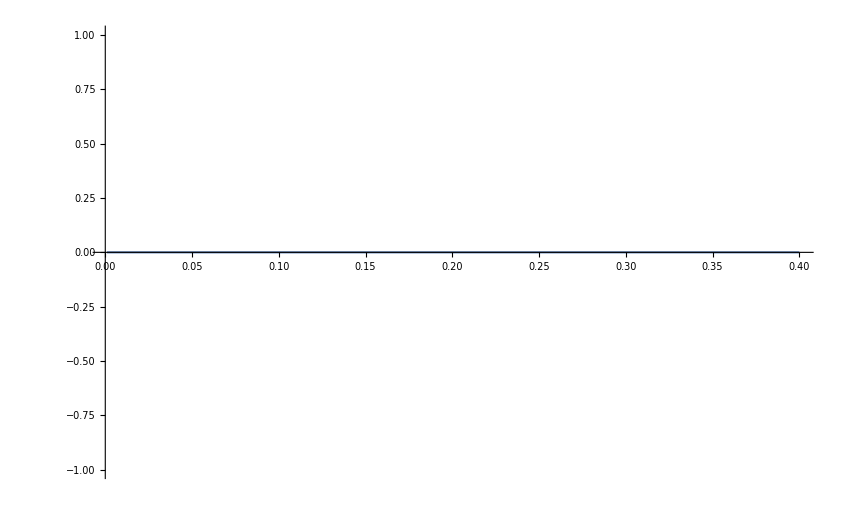

```mathematica
n=12;
i=2200;
t=.;
Kb=1.3806488*10^-16;
Subscript[h, y]=0;
T=0.001;
data=ReadList["statsumm_"<>ToString[n]<>"_"<>ToString[i]<>".dat",{Number,Number,Number}];
z[n_]:=Exp[-(n[[1]]+Subscript[h, x] n[[2]]+Subscript[h, y] n[[3]])/(Kb*T)];(*статсумма*)
statsumm=Total[Map[z,data]];(*получаем знаменатель*)

mm="2.782202745000001"×10^("-13");(*магнитный момент одной частицы*)
mx1[n_]:=n[[2]]*z[n];
my1[n_]:=n[[3]]*z[n];
mx=Total[Map[mx1,data]]/statsumm;
my=Total[Map[my1,data]]/statsumm;
Plot[-mx/mm/(n/2),{Subscript[h, x],0.001,0.4},AxesLabel->{"External field along X axis, Ersted","magnetisation, r.u."},PlotLabel->"Magnetisation level for 12 parts Spin Ice system with L=2200 nm."]
Plot[-my/mm/(n/2),{Subscript[h, x],0.001,0.4}]
```